```mathematica
ClearAll["Global`*"];

(*args=$CommandLine[[3;;]];
Print[args];
var=ToExpression[args[[2]]];
outputDir=args[[3]];
*)
var = 10^0;


(*chemical parameters*)
kinFac = 1;
kAct =     5*10^1; (* mM^-1 s^-1 activation rate of calcium *)
kInact =   5*10^0; (* s^-1 inactivation rate of calcium *)
kTrap =    3*10^2; (* mM^-1 s^-1 trapping rate of calcium by DMNP *)
kRel =     7*10^2; (* s^-1 release rate of calcium by DMNP when light is on*)
kETrap = 2.7*10^3;(* mM^-1 s^-1 trapping rate of calcium by EGTA *)
kERel = 0.5; (* s^-1 release rate of calcium by EGTA *)
kIBind =   kinFac * 1*10^-1; (* mM^-1 s^-1 binding rate of inactivated TCB2 *)
kIUnbind = kinFac * 10^0; (* s^-1 unbinding rate of inactivated TCB2 *)
kABind =   kinFac * 1*10^-1; (* mM^-1 s^-1 binding rate of activated TCB2 *)
kAUnbind = 0; (* s^-1 unbinding rate of activated TCB2 *)
β  = 0.5; (* degradation factor *)

CSat = 5; (* mM, saturation concentration of bound TCB2 *)

DT = 1; (* μm^2/s, diffusion constant for TCB2 *)
DD = 25; (* μm^2/s, diffusion constant for DMNP *)
DE = 180; (* μm^2/s, diffusion constant for EGTA *)
DC = 500 ;(* μm^2/s, diffusion constant for calcium *) 
advectionBool = False;

DFunc[CBtot_]:=1;
(*DFunc[CBtot_]:=((1-CBtot/CSat)/(1+CBtot/CSat))^2;*)

(*initial values*)
CDI0=0 * 2.5; (*mM*)
CDA0=0; (*mM*)
CBI0=0.0000001; (*mM*)
CBA0=0; (*mM*)
CC0=0; (*mM*)
CDst0=0; (*mM*)
CD0=20; (*mM*)
CE0=20; (* mM *)
CEst0 = 0; (* mM *)

(*domain values*)
rMin=1; (*μm*)
rMax=150; (*μm*)
tMax=30; (*s*)
pts=200;

(*light activation values*)
width=5; (*μm,width of gaussian beam*)
r0=75; (*μm,radius of circle*)
len=1; (*s*)
cyc=15+len;
del=0.25; (*s*)

(*mechanical values*)
λ0=1;(*μm^2/s,1st Lame modulus slope*)
μ0=1; (*μm^2/s,2nd Lame modulus slope*)
gMin=0.5; (*shrinking factor of activated TCB2*)


(*import functions*)
Get["/Users/csfloyd/Dropbox/Projects/TCB2Network/Mathematica/MidwayFiles/src/TCB2FunctionsCyl.m"]

(*Plot[iFun[t],{t,0,tMax/10},PlotRange->Full]*)
```

```mathematica
ret=AbsoluteTiming[NDSolve[{pdes,bcs,ics},{CDI[r,t],CDA[r,t],CBI[r,t],CBA[r,t],CC[r,t],CD[r,t],CDst[r,t],CE[r,t],CEst[r,t],u[r,t]},{r,rMin,rMax},{t,0,tMax},Method->{"MethodOfLines","TemporalVariable"->t,
"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->120,"MaxPoints"->pts,"DifferenceOrder"->6},
Method->{"IDA","ImplicitSolver"->{"GMRES"}}},
PrecisionGoal->8,
AccuracyGoal->8,
MaxSteps->1000000]];

Print[ret[[1]]];
sol=ret[[2]];
```

$Aborted

Part::partd: Part specification ret⟦1⟧ is longer than depth of object.

ret⟦1⟧

Part::partd: Part specification ret⟦2⟧ is longer than depth of object.

```mathematica
CDISol[r_,t_]:=Evaluate[CDI[r,t]/.sol];
CDASol[r_,t_]:=Evaluate[CDA[r,t]/.sol];
CBISol[r_,t_]:=Evaluate[CBI[r,t]/.sol];
CBASol[r_,t_]:=Evaluate[CBA[r,t]/.sol];
CCSol[r_,t_]:=Evaluate[CC[r,t]/.sol];
CDSol[r_,t_]:=Evaluate[CD[r,t]/.sol];
CDstSol[r_,t_]:=Evaluate[CDst[r,t]/.sol];
uSol[r_,t_]:=Evaluate[u[r,t]/.sol];
vSol[r_,t_]:=Evaluate[D[uSol[r,tp],tp]/.tp->t];

diffTerm[r_,t_,f_,DD_]:=DD*Evaluate[D[rp*f[rp,t],{rp,2}]/r/.{rp->r}]
diffTermComb[r_,t_,f1_,f2_,DD_]:=DD*Evaluate[D[rp*(f1[rp,t]+f2[rp,t]),{rp,2}]/r/.{rp->r}]
diffFlux[r_,t_,f_,DD_]:=DD*Evaluate[D[f[rp,t],{rp,1}]/.{rp->r}]

sigmoid[x_]:=1/(1+Exp[-x]);
smoothBump[x_,a_,xa_,xb_]:=sigmoid[(x-xa)/a]-sigmoid[(x-xb)/a]
waveFunc[t_,cyc_,len_,del_]:=Sum[smoothBump[t,del,cyc*i,cyc*i+len],{i,0,Floor[tMax/cyc]}];
```

```mathematica
Manipulate[Plot[{CBISol[r,t],CBASol[r,t]},{r,rMin,rMax},PlotRange->{0,CBI0+20}],{t,0,tMax}]
```

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{uSol[r,t]},{r,rMin,rMax},PlotRange->{-2,2}],{t,0,tMax}]
```

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{CBISol[r,t],CBASol[r,t], g[CBASol[r,t],CBISol[r,t]]},{r,rMin,rMax},PlotRange->{0,CBI0+1}],{t,0,tMax}]
```

General::prng: Value of option PlotRange -> {0,1+CBI0} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value rMin in {r,rMin,200} is not a machine-sized real number.

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

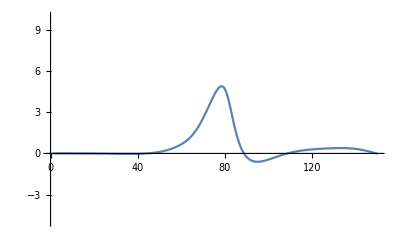

```mathematica
Plot[{uSol[r,tMax]},{r,rMin,rMax},PlotRange->{-5,10}]
```

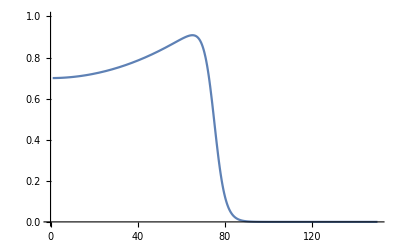

```mathematica
off = .7;
Plot[(off +(1-off)(r/r0)^2)spaceFunc[r,r0,width],{r,rMin,rMax},PlotRange->{0,1}]
```

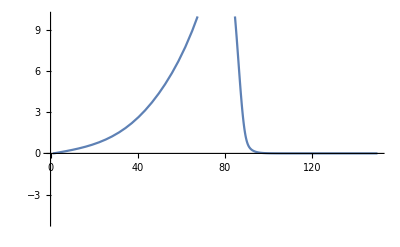

```mathematica
Plot[{uSol[r,tMax]},{r,rMin,rMax},PlotRange->{-5,10}]
```

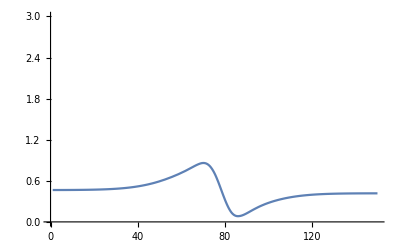

```mathematica
Plot[{CBISol[r,130]},{r,xMin,xMax},PlotRange->{0,3}]
```

```mathematica
InterpFunction[funcN_,rMinN_,rMaxN_,tMaxN_]:=Module[{func = funcN, rMin = rMinN, rMax = rMaxN, tMax = tMaxN},
	intDat=Table[
	{{r,t},Evaluate[func[r,t][[1]]]}
	,{r,rMin,rMax,1.},{t,0.,tMax,1.}];
	dn=Flatten[Flatten[intDat,1],1];
	fN=Interpolation[dn,InterpolationOrder->2]
]
 
intDat=Table[
	{{r,t},Evaluate[uSol[r,t][[1]]]}
	,{r,rMin,rMax,1.},{t,0.,tMax,1.}];
dn=Flatten[Flatten[intDat,1],1];
dn=Flatten[intDat,1];
fN=Interpolation[dn,InterpolationOrder->2]
```

```mathematica
Manipulate[Plot[{diffTerm[r,t,CDASol,DTA],diffTerm[r,t,CDISol,DT],diffTerm[r,t,CDASol,DTA]+diffTerm[r,t,CDISol,DT],0.5*waveFunc[t,cyc,len,del]},{r,xMin,xMax},PlotRange->{-.5,.5}],{t,0,tMax,1}]
```

Plot::plln: Limiting value xMin in {r,xMin,300} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,300} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,300} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,300} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{CBASol[r,t]+CBISol[r,t],pA[CBASol[r,t],CBISol[r,t]]},{r,xMin,xMax},PlotRange->{-1,3}],{t,0,tMax}]
```

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{CDASol[r,t]+CDISol[r,t],CDASol[r,t],CDISol[r,t]},{r,xMin,xMax},PlotRange->{-1,3}],{t,0,tMax}]
```

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,300} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{CBASol[r,t]+CBISol[r,t],CBASol[r,t],CBISol[r,t]},{r,xMin,xMax},PlotRange->{-1,3}],{t,0,tMax}]
```

Plot::plln: Limiting value xMin in {r,xMin,300} is not a machine-sized real number.

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{uSol[r,t],5*waveFunc[t,cyc,len,del]},{r,xMin,xMax},PlotRange->{-5,10}],{t,0,tMax}]
```

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{vSol[r,t],0.5*waveFunc[t,cyc,len,del]},{r,xMin,xMax},PlotRange->{-0.5,0.5}],{t,0,tMax}]
```

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{CCSol[r,t],CDSol[r,t]},{r,xMin,xMax},PlotRange->{0,20}],{t,0,tMax}]
```

Plot::plln: Limiting value xMin in {r,xMin,xMax} is not a machine-sized real number.

```mathematica
ClearAll["Global`*"];2 μ0*((CBA+CBI)*(D[u[r],{r,2}]+1/r D[u[r],r]-u[r]/r^2-1/2 gp))+λ0*((CBA+CBI)*(D[u[r],{r,2}]+1/r D[u[r],r]-u[r]/r^2-gp))//FullSimplify
```

((CBA+CBI) (-gp r^2 (λ0+μ0)-(λ0+2 μ0) (u[r]-r (u'[r]+r u''[r]))))/r^2

```mathematica
Collect[-gp r^2 (λ0+μ0)-(λ0+2 μ0) (u[r]-r (u'[r]+r u''[r])),{μ0,λ0}]
```

λ0 (-gp r^2-u[r]+r (u'[r]+r u''[r]))+μ0 (-gp r^2-2 (u[r]-r (u'[r]+r u''[r])))

```mathematica
D[1/r D[r*u[r],r],r]//Simplify
```

-u[r]/r^2+u'[r]/r+u''[r]

```mathematica
D[r*f[r],{r,2}]/r//Simplify
```

(2 f'[r])/r+f''[r]

```mathematica
D[r*D[f[r],r],r]/r//Simplify
```

f'[r]/r+f''[r]